# TuGamesView2d : A basic Introduction

by Holger I.Meinhardt, University of Karlsruhe (KIT)

E-mail: Holger.Meinhardt@wiwi.uni-karlsruhe.de

## General Remarks

In order to depict game solutions for three person games only at least two packages must be loaded. Firstly, we have to load the package "CooperativeGames`" written by M.Carter to provide some basic functions, then the package "TuGames`" has to be loaded to provide the main functionality of our game theory software under Mathematica. Both packages provide a small set of functions to plot two dimensional game solutions. On the one hand there are the functions Draw[] in "CooperativeGames`", and FilledCore[] in the package "TuGames`" to plot the core for three person games under Mathematica version 5. x and smaller only. On the other hand due to the fundamental change in the graphic concept since Mathematica version 6 we have provided some additions and changes to adjust our package to these new graphical development. For this reason we have written the functions FilledCoreV6[], StrongEpsCore2d[], and AnimationKernelProperty2d[], whereas the former function is an upgrade of the function FilledCore[]. The second plots the strong epsilon core in connection with some other solution concept from game theory, and the latter evaluates a small movie to visualize the geometric property of the kernel/nucleolus. However, to use the old graphic concept of Mathematica version 5. x one has to load the package “<< Version5`Graphics`”. The last command restores the old graphic concept of Mathematica. For a proper functionality it is important to note that one cannot mix in one notebook both graphic concepts. One has to made a decision which graphic concept should be used. Moreover, the front-end of Mathematica 5. x cannot handle graphic objects generated by Mathematica 6. x and higher, in this case one must expect a crash of the front-end of Mathematica 5. x. Notice that all graphical extensions require the cddmathlink libraries written by Komei Fukuda. The cddmathlink libraries can be compiled for all platforms, we expect, therefore, that the graphical extensions should not be anymore restricted to UNIX platforms in contrast to the old version of "TuGames`". For more details see the section requirements in the TuGames.m file.

## Getting Started

If everything is installed properly, we can now load the above mentioned packages while typing

```mathematica
Needs["TUG`"];
```

===================================================

Loading Package 'TuGames' for Unix

===================================================

TuGames V3.0.3 by Holger I. Meinhardt

Release Date: 17.02.2022

Program runs under Mathematica Version 12.0 or later

Version 12.x or higher is recommended

===================================================

===================================================

Package 'TuGames' loaded

===================================================

For loading the cddmathlink libraries, the working directory is internally set to the directory where the cddmathlink libraries are installed, to restore the original path from which Mathematica was started, we reset the directory by

```mathematica
(* ResetDirectory[]; *)
```

This is required when one has the intention to export some of the generated graphics and to find them again in the current working directory. Otherwise, the exported graphics are copied to the installation directory of the cddmathlink libraries, which would be in this case the current working directory.

Now we are in the position to define a three person example game, which is done by providing the player set T, and the valuation of the coalitions, which is given by a vector of coalition values. These information are sufficient to specify a transferable utility game. This is done by determining the 8 components of the list “clv”, and the three player set given by the variable T. The function that defines the game for us is called DefineGame[]. By default this function defines the game in rational numbers rather than by floating point numbers. In order to get a game definition in floating point numbers the option “RationalApproximate” must be set to “False”.

```mathematica
clv={0,0,0,0,90,100,120,220};
```

```mathematica
T={1,2,3}
```

{1,2,3}

```mathematica
ExpGame01:=DefineGame[T,clv];
```

To test that the game has been defined properly, we verify first some game properties.

```mathematica
ConvexQ[ExpGame01]
```

True

```mathematica
CoreQ[ExpGame01]
```

True

```mathematica
AvConvexQ[ExpGame01]
```

True

```mathematica
AverageConvexQ[ExpGame01]
```

True

For checking that the cddmathlink libraries are installed correctly we invoke the corresponding function names

```mathematica
crv=CddGmpVerticesCore[ExpGame01]
```

{{0,120,100},{0,90,130},{100,0,120},{100,120,0},{90,0,130}}

```mathematica
crv1=CddGmpVerticesCore[ExpGame01,RationalExact->False]
```

{{0,90.,130.},{0,120.,100.},{90.,0,130.},{100.,0,120.},{100.,120.,0}}

```mathematica
crv2=CddVerticesCore[ExpGame01]
```

{{0,120,100},{0,90,130},{100,0,120},{100,120,0},{90,0,130}}

```mathematica
crv3=CddVerticesCore[ExpGame01,RationalExact->False]
```

{{0.,90.,130.},{0.,120.,100.},{90.,0.,130.},{100.,0.,120.},{100.,120.,-1.33227×10^-14}}

Next some well known game solutions are computed

```mathematica
ker=Kernel[ExpGame01]
```

{170/3,230/3,260/3}

```mathematica
shv=ShapleyValue[ExpGame01]
```

{65,75,80}

```mathematica
mnuc=ModifiedNucleolus[ExpGame01]
```

{170/3,230/3,260/3}

```mathematica
nuc=Nucleolus[ExpGame01]
```

{170/3,230/3,260/3}

```mathematica
bcQ=BelongToCoreQ[ExpGame01,shv]
```

True

```mathematica
PreKernelSolution[ExpGame01]
```

{170/3,230/3,260/3}

```mathematica
PreKernelElement[ExpGame01]
```

{170/3,230/3,260/3}

```mathematica
PreKernelSolution[ExpGame01,crv]
```

{{170/3,230/3,260/3}}

```mathematica
PreKernelElement[ExpGame01,crv]
```

{{170/3,230/3,260/3}}

## Core Plot2d

In this section we demonstrate how the core can be plotted in connection with some important game solutions. To get some overview about the set of options with which the function FilledCoreV6[] can be called for, type simply

```mathematica
Options[FilledCoreV6]
```

{DisplayLegend→True,FigureSize→500,PreImpSet→True,Silent→False}

We provide a very small set of options to control the appearance of the two dimensional core graphics. Notice, that the core graphic will be always plotted in connection with the Shapley value, kernel/nucleolus and pre - kernel/pre - nucleolus. Moreover, the user has no influence to fade out the vertices labeling. However, it is allowed to fade out the legend in the plot, changing the figure/image size and to switch - on a monitoring mode to follow the progress of evaluation. By default the legend mode is always activated, the figure size is set to "500", and the verbosity is deactivated. Therefore, when invoking FilledCoreV6[] with the sole argument name of the game, then we get something like this

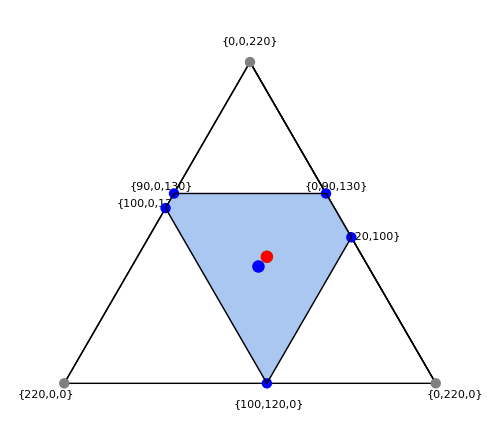

```mathematica
fig01=FilledCoreV6[ExpGame01]
```

From the core graphic above we learn that the core area is always shaded blue, which cannot be changed without editing the package file "TuGames.m".

In case that the user want to deactivate the legend mode, the option "DisplayLegend" must be set to "False", and the function FilledCoreV6[] must be called with two arguments as in the demonstration coming next

```mathematica
fig02=FilledCoreV6[ExpGame01,DisplayLegend->False]
```

-Graphics-

To export the graphics above, uncomment the following line

```mathematica
(* Export["core2d01.jpg",Style[fig01,Magnification->1.5]];
Export["core2d02.png",Style[fig02,Magnification->1.5]];*)
```

## Strong Epsilon Core Plot2d

Similar to the FilledCoreV6[] graphic command, the command to plot the strong epsilon core allows only to set the epsilon value, the figure/image size, and to switch on the labeling on or off for the vertices of the strong epsilon core, which is always depicted as skeleton. To get an overview of the option set of this function, type

```mathematica
Options[StrongEpsCore2d]
```

{EpsilonValue→5,FigureSize→500,Labeling→True}

As we observe by the above example the default value of the strong epsilon core is set to "5", the figure size is set to "500", and the labeling of the vertices is switched on.

We demonstrate next how we can plot a strong epsilon core with epsilon value 20 in connection with the core, the imputation set, and the above game solutions. For doing so, we have to call the command StrongEpsCore2d[] with two arguments while updating the value of the option "EpsilonValue". Thus, we invoke

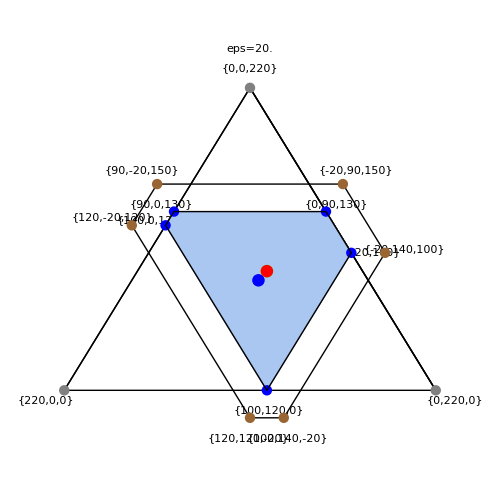

```mathematica
fig03=StrongEpsCore2d[ExpGame01,EpsilonValue->20]
```

Now, we enlarge the epsilon value further to "30".

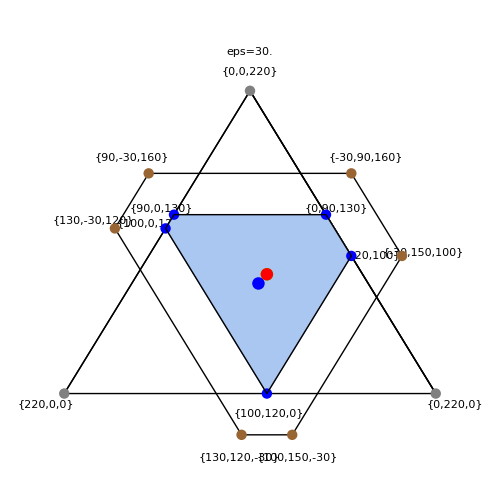

```mathematica
fig04=StrongEpsCore2d[ExpGame01,EpsilonValue->30]
```

When the labeling of the vertices of the strong epsilon core should be deactivated the above graphics look like

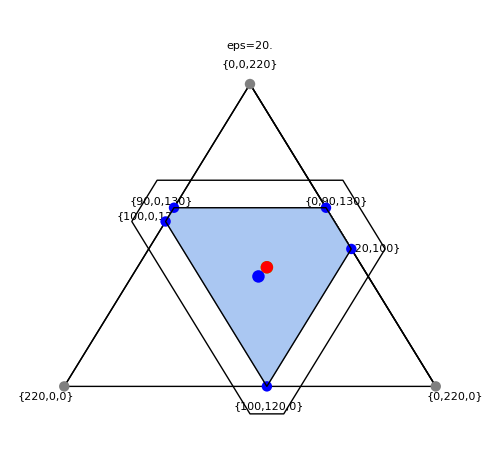

```mathematica
fig05=StrongEpsCore2d[ExpGame01,EpsilonValue->20,Labeling->False]
```

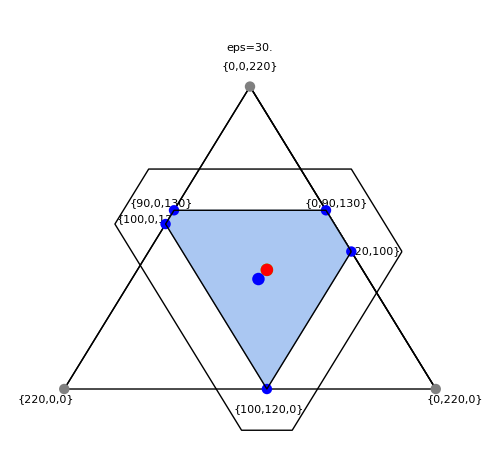

```mathematica
fig06=StrongEpsCore2d[ExpGame01,EpsilonValue->30,Labeling->False]
```

## Animate Geometric Property of the Kernel/Nucleolus

After we have learned how to depict two dimensional game solutions, a few words are in order to understand how to use the animation command to visualize the geometric property of the kernel/nucleolus. The function AnimationKernelProperty2d[] generates in a first step a list of frames which can later on be rendered by the front-end of Mathematica having the side-effect that the frames can be exported much more easier than relying on the Mathematica built-in command Animate[] or Manipulate[]. When calling AnimationKernelProperty2d[] with a semicolon the rendering process of the front-end is suppressed, only the graphical primitives have been produced. This is done to get some of the old graphical behavior back to run more smoothly an animation. We find it more convenient to produce all frames at the beginning, rather than to reevaluating everything from scratch. But before we discuss this behavior in more detail, we want discuss some crucial options, and with which values they can be invoked. Information about the set of options can be attained while invoking

```mathematica
Options[AnimationKernelProperty2d]
```

{UpperCritVal→{5},LowerCritVal→{},IncSize→{-1/4},FigureSize→500,UseManipulate→False}

Here, the first option "UpperCritVal" specifies the largest strong epsilon core we want to consider in the forthcoming animation. In this example the value is chosen to be "30", its default value is "5". However, the option "LowerCritVal" specifies the smallest strong epsilon core we want to depict. We notice that this value is unset or empty indicating that the least core is used by default. Furthermore, the option "IncSize" determines the increment steps to shrink the epsilon value. Finally, setting the options "UseManipulate" to "False" indicates that we want produce a list of frames rather than an interactive graphic.

Invoking the animation command, we have generated in total 147 frames which can be animated later.

```mathematica
a1=AnimationKernelProperty2d[ExpGame01,UpperCritVal->{30},LowerCritVal->{},IncSize->{-(1/2)}];
```

```mathematica
Length[a1]
```

147

These frames allow us to produce a QuickTime movie of 6 seconds. In order to get a longer and smoother movie more frames must be produced, this can be done while increasing the IncSize for instance from (-1/4) to (-1/20). How we can do that is postponed for while, first we want to demonstrate that with the variable a1 that grasp all frame information, we are able to run an animation while invoking the command

```mathematica
ListAnimate[a1,1]
```

Moreover, as we can seen next, the advantage of producing a list of frames allow us also to restore the old animation behavior of Mathematica 5. x and lower. For getting its old behavior back we have first to unravel the list in which the graphics are wrapped by Map[Print, a1]. This renders all 147 frames, selecting all the cells containing a graphic object and collapsing the cells let us allow to animate a movie within the notebook while selecting from the Menu the items Graphics -> Rendering -> Animate Selected Graphics.

-Graphics-

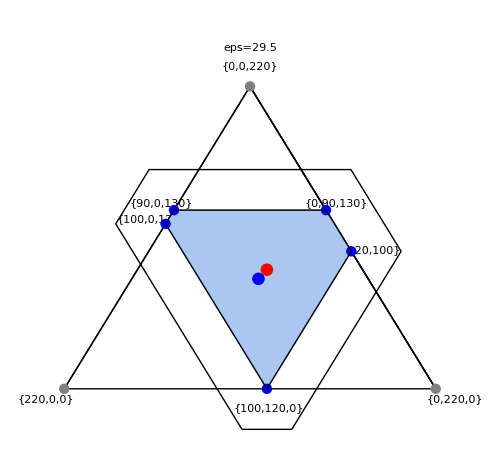

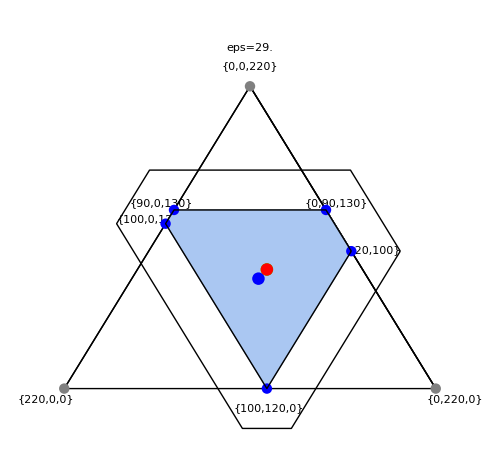

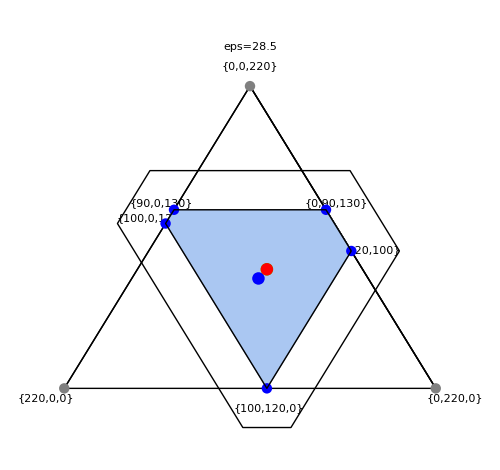

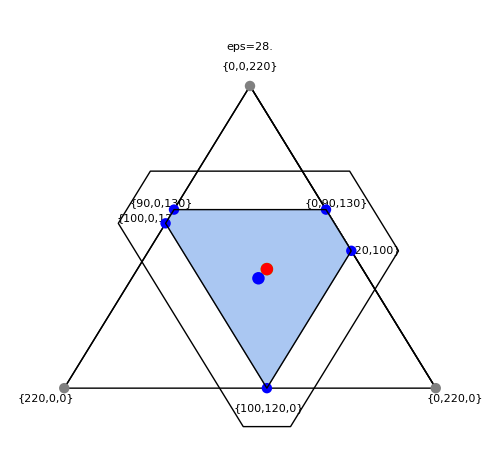

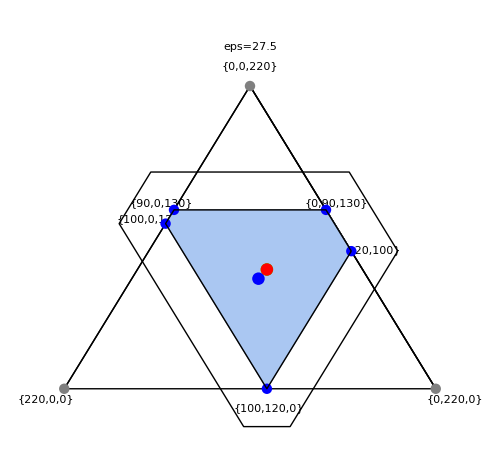

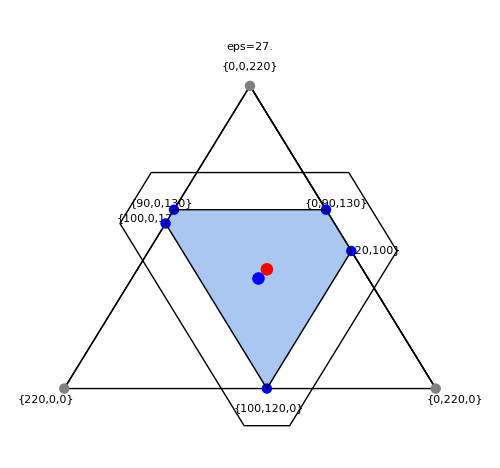

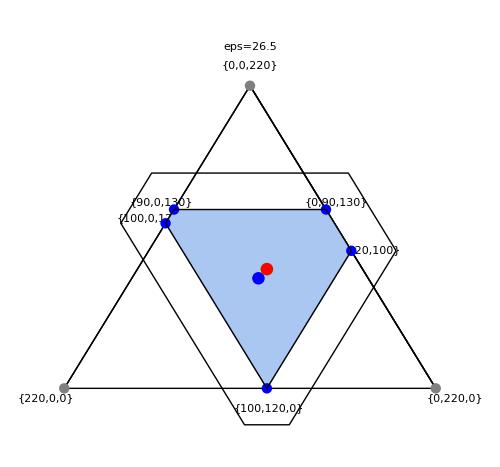

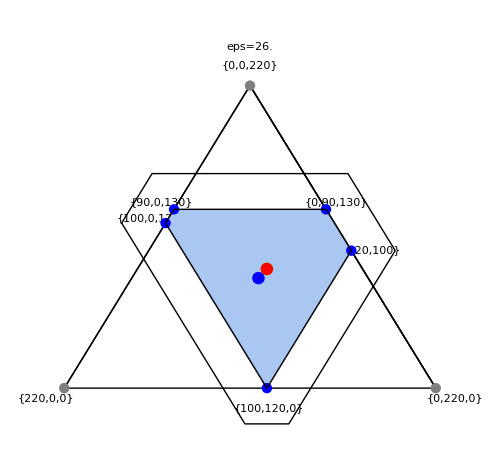

-Graphics-

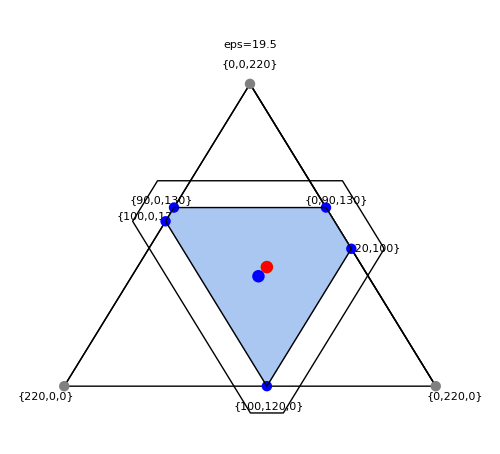

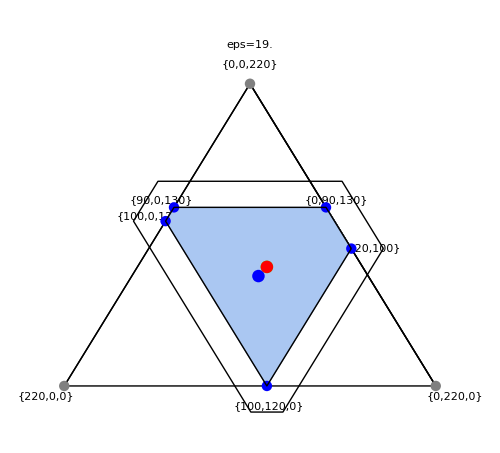

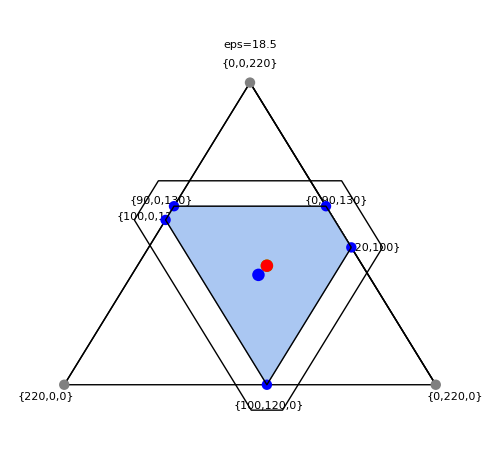

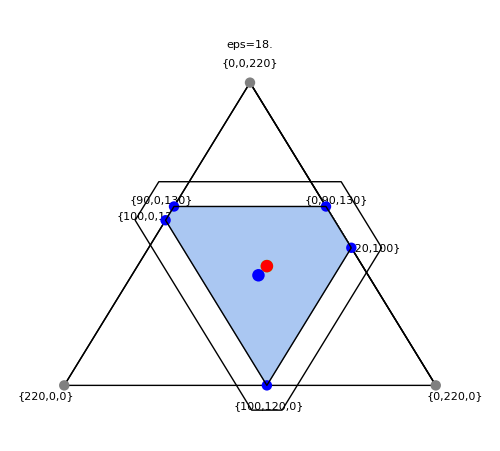

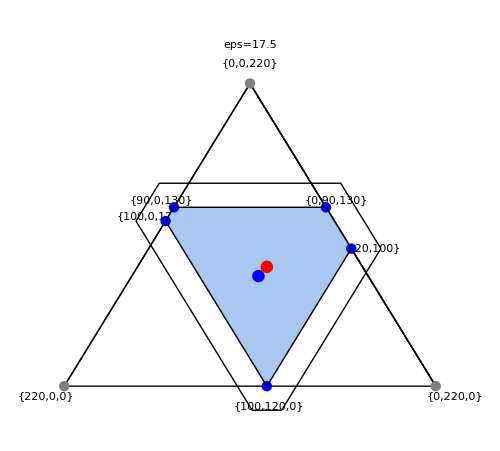

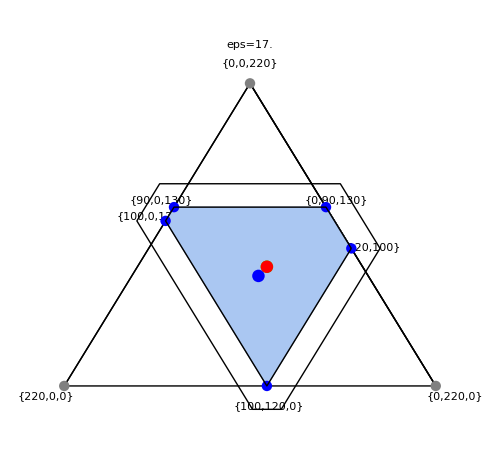

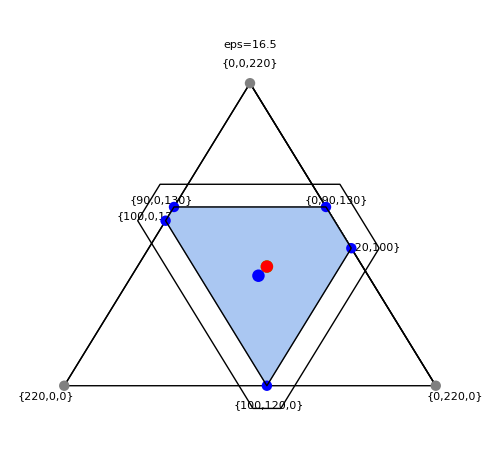

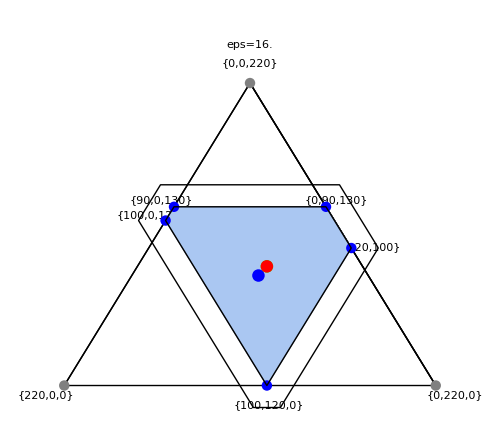

-Graphics-

-Graphics-

-Graphics-

«22 more identical outputs»

```mathematica
Map[Print,a1];
```

After having discussed these properties, we want come back to the question, how we can produce QuickTime movies. First export all frames in jpg-format by uncomment the function below, which we have borrowed from Jens Noeckel

```mathematica
exportFrames[baseName_,a_,ext_:"jpg"]:=Module[{l=Length[a],d},d=Length@IntegerDigits[l];
Table[Export[baseName<>IntegerString[i,10,d]<>"."<>ext,Style[a[[i]],Magnification->1.5]],{i,l}]]
```

To speed up the procedure you can also replace the Table[] command by ParallelTable[], if you have a multicore processor. Then invoke, for instance, exportFrames["Exp01krmovie", a1]

Finally, from the command line of your operating system type, for instance, 
ffmpeg -sameq -i Exp01krmovie%02d.jpg Exp01krmovie1.mp4

or alternatively

avconv -i Exp01krmovie%02d.jpg -q 6 Exp01krmovie1.mp4

in case that you have less than 100 frames, however, up to 999 frames use

ffmpeg -sameq -i Exp01krmovie%03d.jpg Exp01krmovie1.mp4

or alternatively

avconv -i Exp01krmovie%03d.jpg -q 6 Exp01krmovie1.mp4

For additional information or other movie formats consult the very nice website of Jens Noeckel, which is available under the URL

http : // pages.uoregon.edu/noeckel/MathematicaGraphics.html

The function AnimationKernelProperty2d[] allows also to generate an interactive graphic with the Manipulate command. For doing so, it is just enough to set the option "UseManipulate" to "True", then it is possible to manipulate interactively the strong epsilon value of the graphic. Notice that in this case, everything must be recomputed/rerendered from scratch whenever you update the epsilon value with the slider or the control wrapper. In addition, note that the variable a2 contains a dynamic object that is considered by Mathematica potentially as unsafe. For this reason, we have deleted the interactive graphic from this notebook. To get it back, it is just enough to reevaluate the cells below

```mathematica
exportFrames["Exp01krmovie",a1]
```

```mathematica
a2=AnimationKernelProperty2d[ExpGame01,UpperCritVal->{30},LowerCritVal->{},IncSize->{-(1/2)},UseManipulate->True];
```

```mathematica
Length[a2]
```

2

```mathematica
a2
```